```mathematica
SetDirectory["C:\\Users\\tak\\Desktop\\graph_search"]
```

C:\Users\tak\Desktop\graph_search

## DFS

```mathematica
Module[{i=1},
Do[Export["dfs_"<>ToString[i++]<>".png",g],
{g,
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,8,7,10},visited/@{10},visit/@{2,1,4},visited/@{4},visit/@{3,9},visited/@{9,3,1,2,7,8,6,5}]]
]
}];
i-1
]
```

21

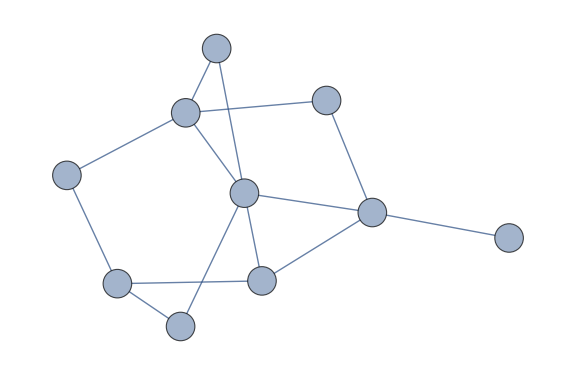
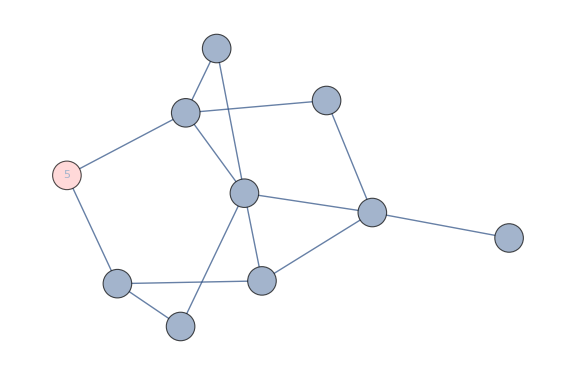
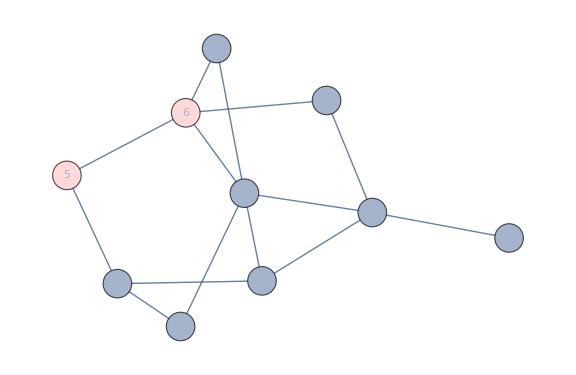
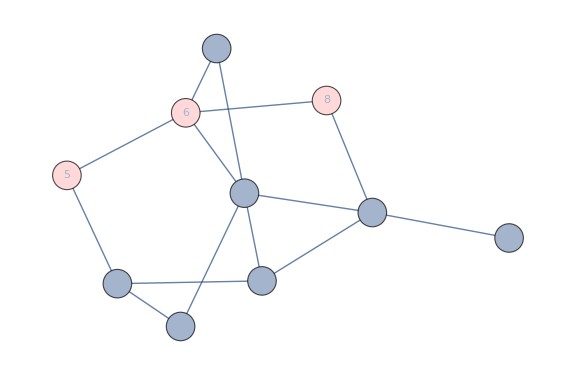
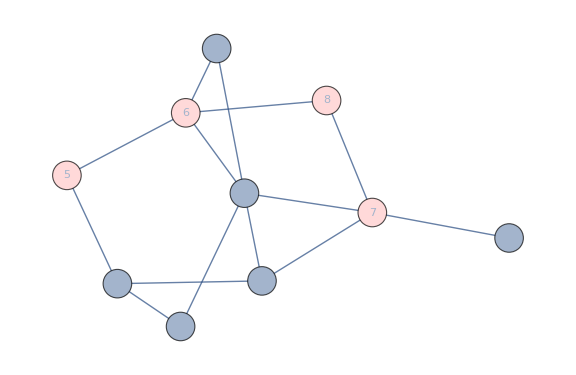
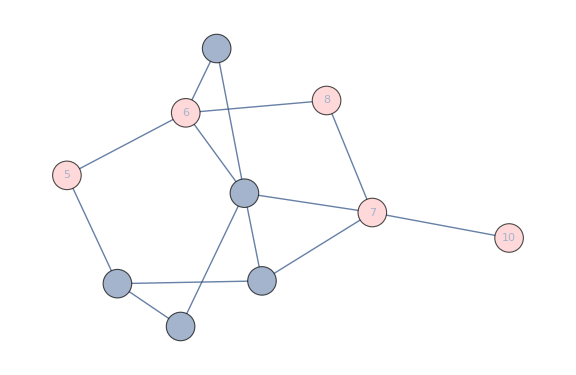
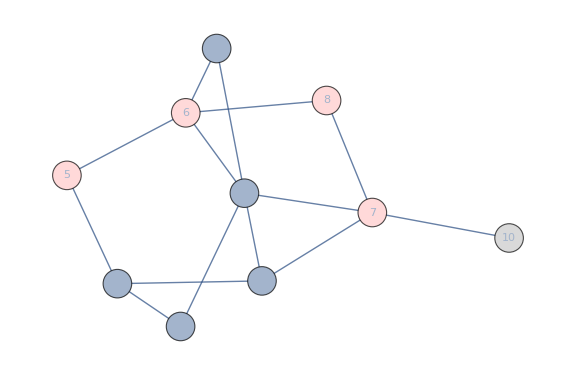
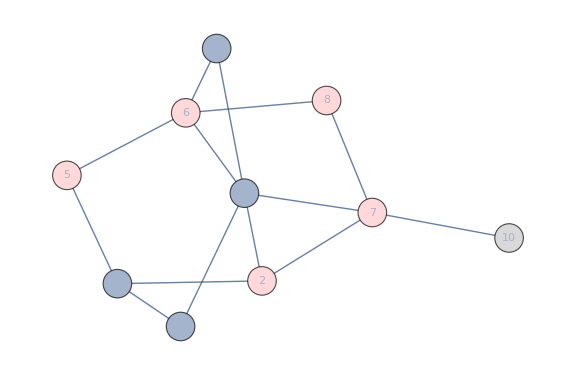

```mathematica
Column[Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,8,7,10},visited/@{10},visit/@{2,1,4},visited/@{4},visit/@{3,9},visited/@{9,3,1,2,7,8,6,5}]]
]]
```

```mathematica
Export["dfs.gif",ListAnimate[
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,8,7,10},visited/@{10},visit/@{2,1,4},visited/@{4},visit/@{3,9},visited/@{9,3,1,2,7,8,6,5}]]
],ControlPlacement->Top
]]
```

dfs.gif

## Topological Sort

```mathematica
Module[{i=1},
Do[Export["toposort_"<>ToString[i++]<>".png",g],
{g,
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{4,5,6},visited/@{6,5},visit/@{8},visited/@{8,4},visit/@{3,7},visited/@{7,3},visit/@{1,2},visited/@{2,1}]]
]
}];
i-1
]
```

17

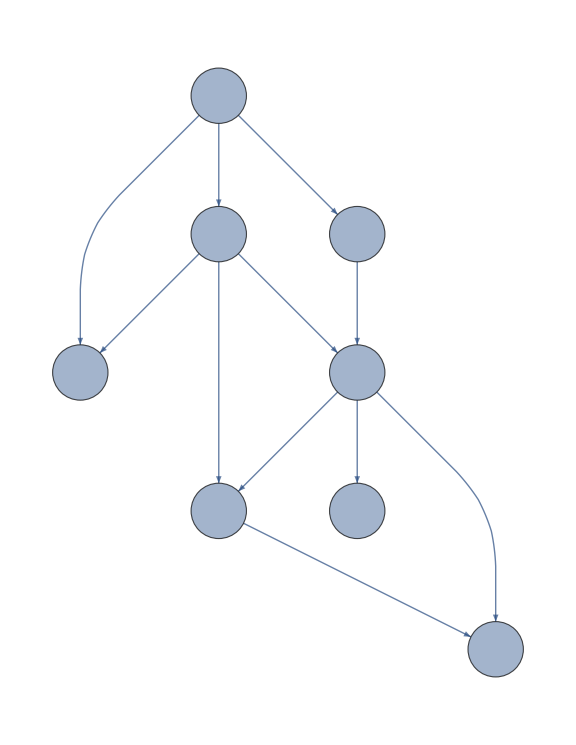
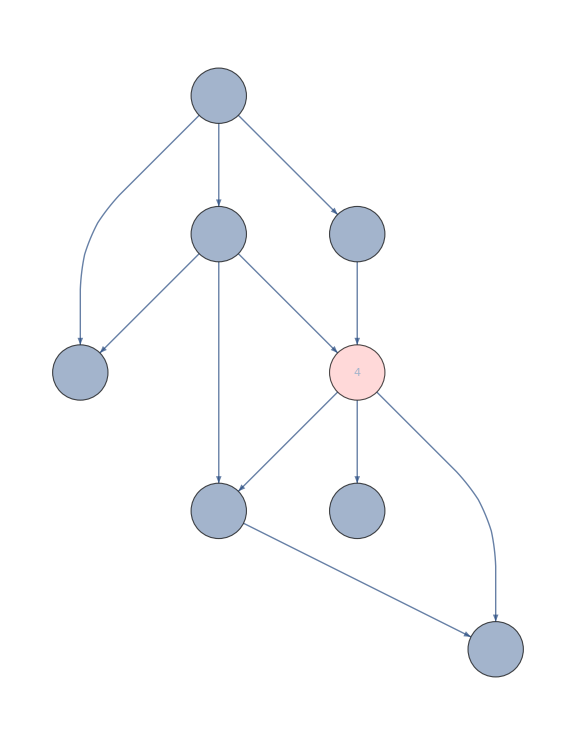
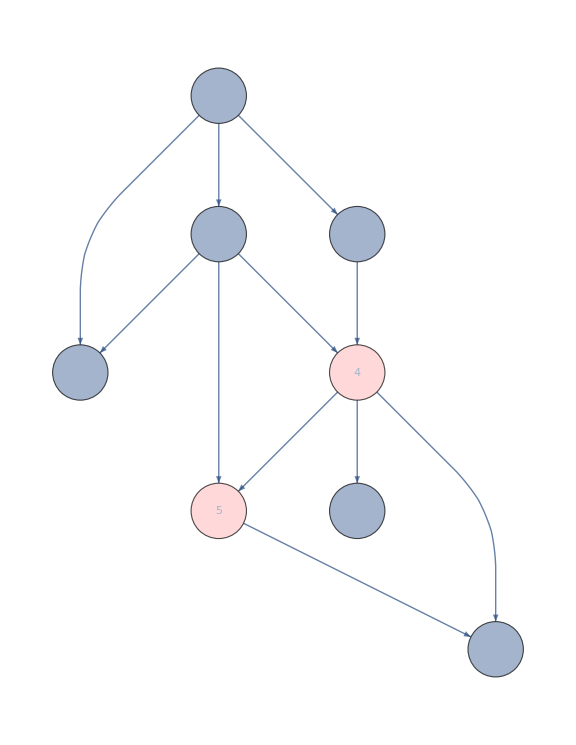
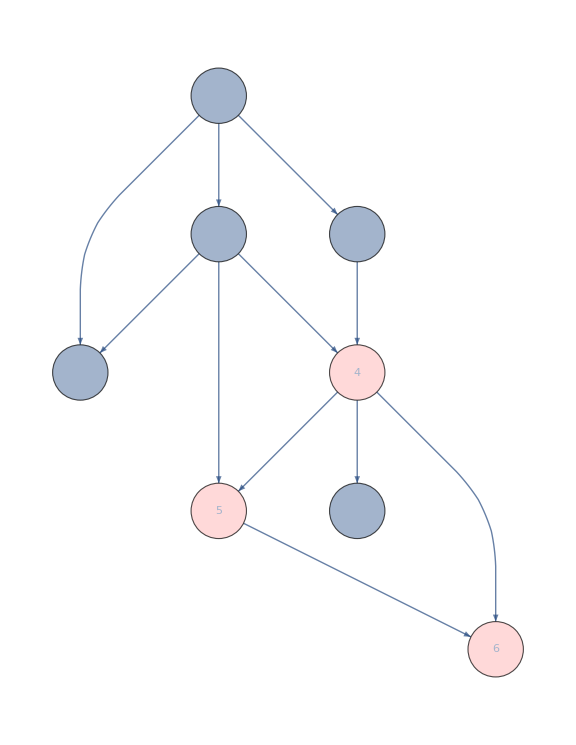
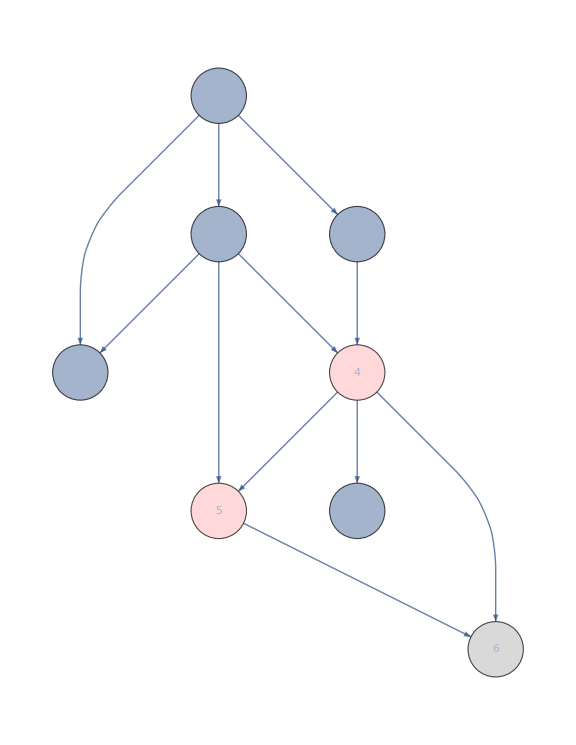
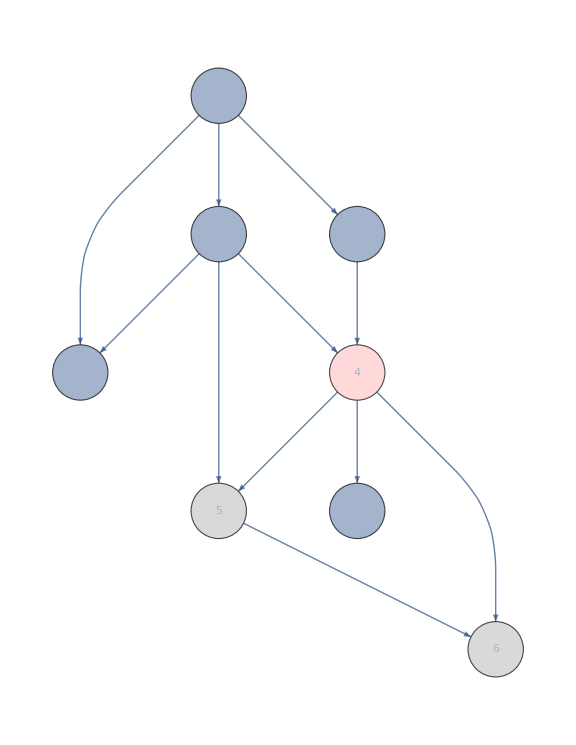
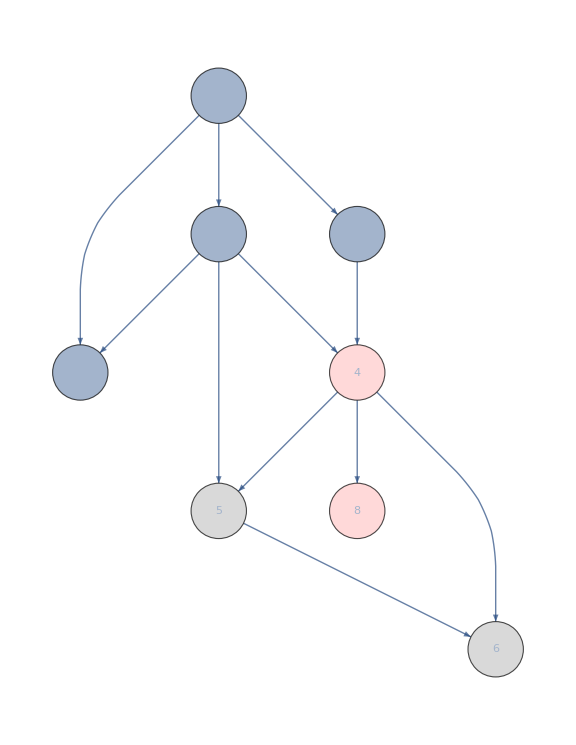
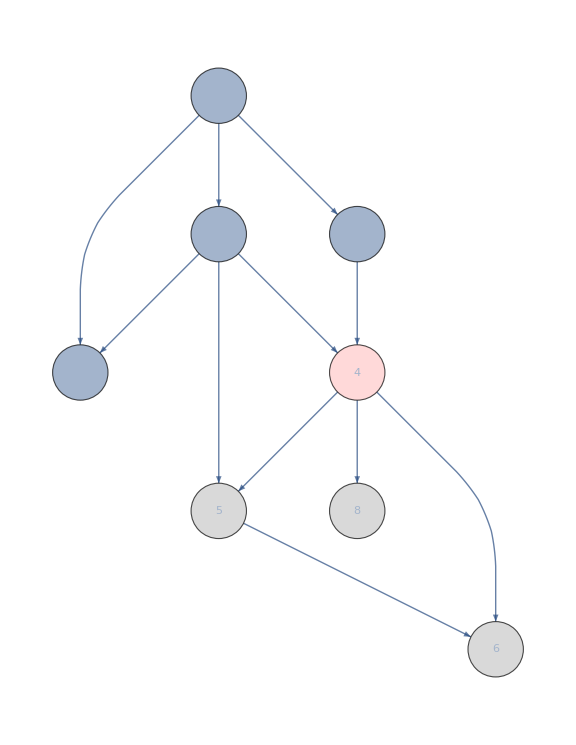

```mathematica
Column@
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{4,5,6},visited/@{6,5},visit/@{8},visited/@{8,4},visit/@{3,7},visited/@{7,3},visit/@{1,2},visited/@{2,1}]]
]
```

```mathematica
Export["toposort.gif",ListAnimate[
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{4,5,6},visited/@{6,5},visit/@{8},visited/@{8,4},visit/@{3,7},visited/@{7,3},visit/@{1,2},visited/@{2,1}]]
],ControlPlacement->Top
]]
```

toposort.gif

## BFS

```mathematica
Module[{i=1},
Do[Export["bfs_"<>ToString[i++]<>".png",g],
{g,
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,9},visited/@{5},visit/@{4,8,1},visited/@{6},visit/@{2,3},visited/@{9,4},visit/@{7},visited/@{8,1,2,3},visit/@{10},visited/@{7,10}]]
]
}];
i-1
]
```

21

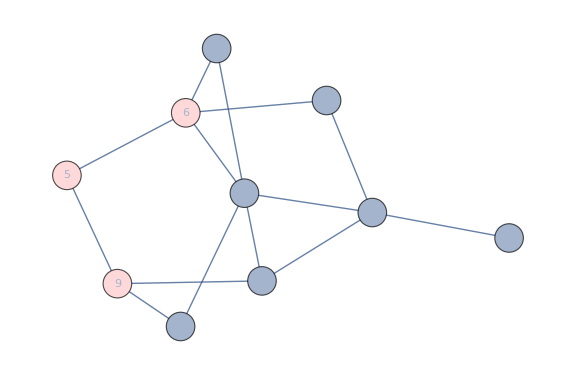
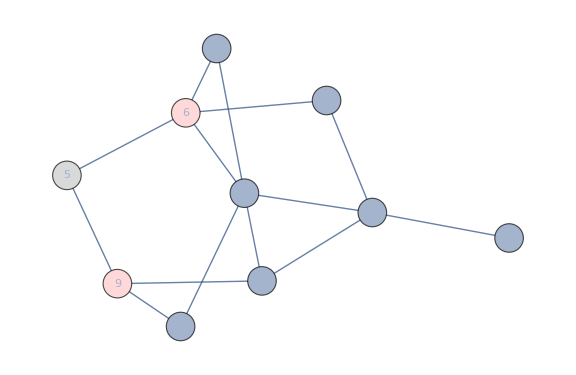
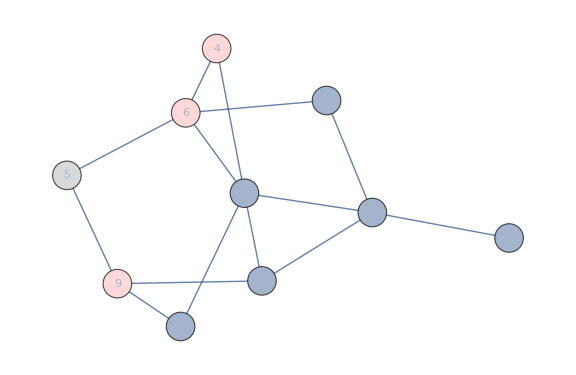
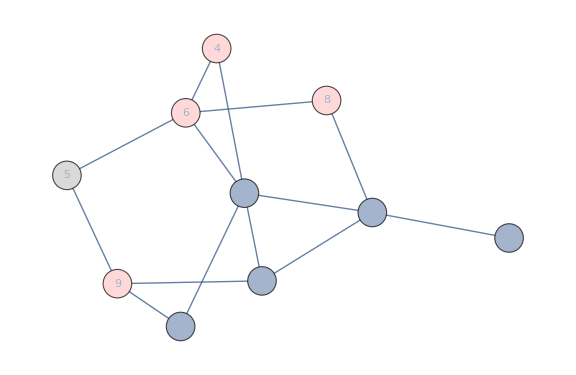
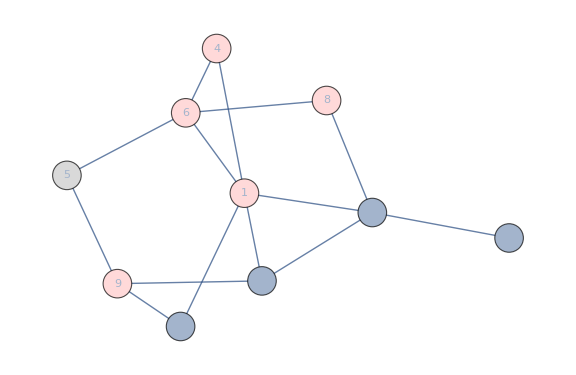
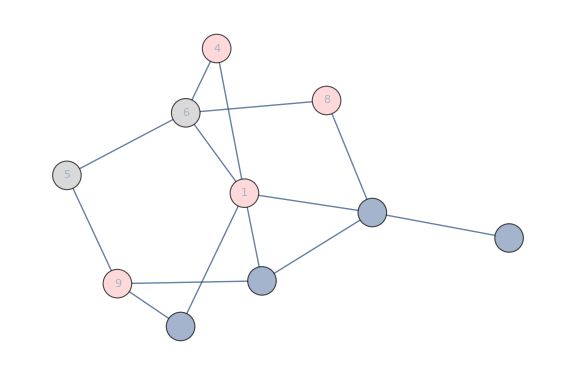
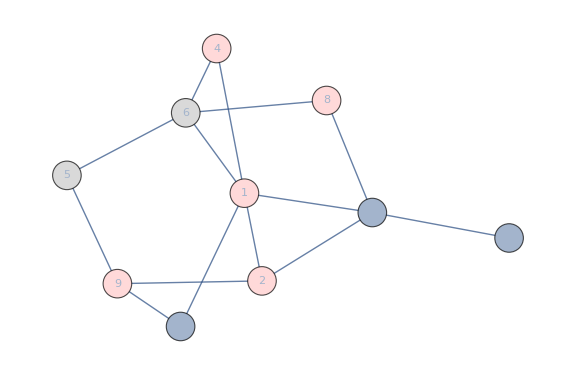
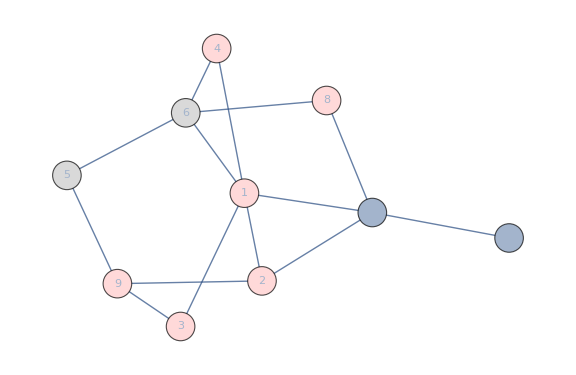
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Column@Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,9},visited/@{5},visit/@{4,8,1},visited/@{6},visit/@{2,3},visited/@{9,4},visit/@{7},visited/@{8,1,2,3},visit/@{10},visited/@{7,10}]]
]
```

```mathematica
Export["bfs.gif",ListAnimate[
Module[{visit=Function[#->LightRed],visited=Function[#->LightGray]},
GraphPlot[-Graphics-,VertexStyle->#,options]&/@FoldList[Append,{},Join[visit/@{5,6,9},visited/@{5},visit/@{4,8,1},visited/@{6},visit/@{2,3},visited/@{9,4},visit/@{7},visited/@{8,1,2,3},visit/@{10},visited/@{7,10}]]
],ControlPlacement->Top
]]
```

bfs.gif